# 29: Shifted QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

Real world versions of QR eigenvalue algorithms do more than one shift at a time and these shifts are implemented implicitly.

## Single Shift

We implemented a single shift μ_1as follows
	H | - | μ_1 I | = | Q_1.R_1 |   |  
  |   | H_1 | = | R_1.Q_1 | + | μ_1 I

Remember this QR step does not change the eigen values since
	  | H-μ_1 I | = | Q_1.R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I) | = | R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | R_1.Q_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
In words, the single shift QR algorithm implements an orthogonal similarity transformation of H-μ_1 I. This is the same as implementing the same similarity transformation (defined by Q_1) on H
	  | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
⟹ | (Q_1)ᵀ.H.Q_1-μ_1(Q_1)ᵀ.Q_1 | = | H_1-μ_1 I
⟹ | (Q_1)ᵀ.H.Q_1 | = | H_1
All we really need is Q_1! There are several ways to compute Q_1. In exact arithmetic they must all be “essentially” the same since the QR decomposition is “essentially” unique.  Of course, we know some are more stable than others. Some are more work than others!

For instance we can compute all of Q (using say a QR decomposition) before we start doing anything else or we could do the columns (and matching rows) with tiny Given’s rotations one at a time.  The second alternative, doing the columns and row as you go, is called an implicit shift and is much less work.   Here is a function that applies a sequence of tiny 2×2 Givens rotations down the diagonal of a tridiagonal symmetric T. 
	 T=(α_1 | β_1 |   |   |   |  
β_1 | α_2 | β_2 |   |   |  
  | β_2 | α_3 | β_3 |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | β_(m-2) | α_(m-1) | β_(m-1)
  |   |   |   | β_(m-1) | α_m)
Just as a reminder 
	(p_1 | p_2
-p_2 | p_1).(α_k | β_k
β_k | α_(k+1))=(? | ?
0 | ?)
iff -p_2 α_k+p_1 β_k=0.  One of the two unit vectors doing this is 
	{p_1,p_2}=Normalize[{α_k,β_k}]

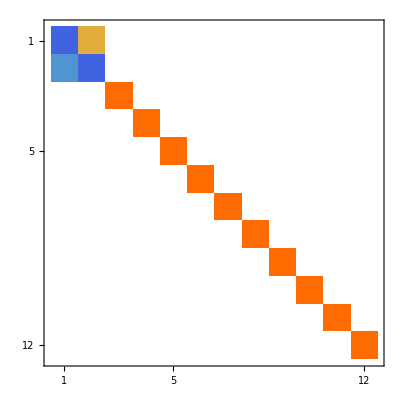
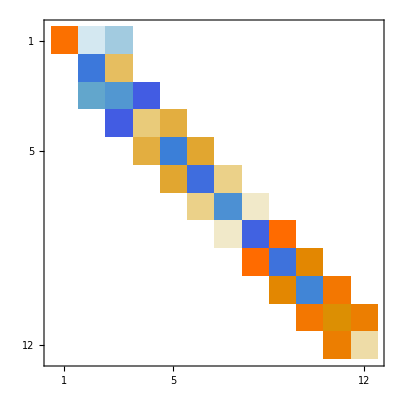
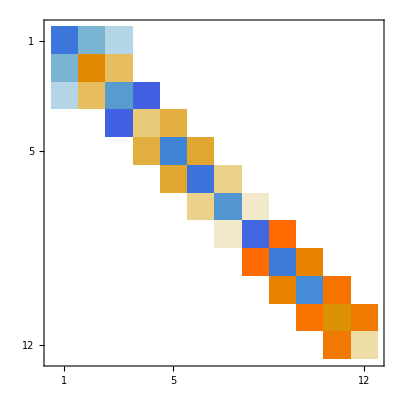

```mathematica
m=12;
α=RandomReal[{-1,1},m];
β=RandomReal[{-1,1},m-1];
T=SparseArray[{
Band[{1,1}]->α,
Band[{1,2}]->β,
Band[{2,1}]->β}];
Id=SparseArray[Band[{1,1}]->1,{m,m}];
k=1;
{p1,p2}= Normalize[{T⟦k,k⟧,T⟦k+1,k⟧}];
Q=Id; 
Q⟦k;;k+1,k;;k+1⟧=({{p1, p2}, {-p2, p1}});
Map[MatrixPlot,{Q,Q.T,Q.T.Qᵀ}]
```

```mathematica
m=4;
T=SparseArray[{
Band[{1,1}]->Array[Subscript[α,#]-μ&,m],
Band[{1,2}]->Array[Subscript[β,#]&,m-1],
Band[{2,1}]->Array[Subscript[β,#]&,m-1]
},{m,m}]
MatrixForm[T]
G1=SparseArray[Band[{1,1}]->1,{m,m}];
{i,j}={1,2};
G1⟦{i,j},{i,j}⟧={{Subscript[p, 1],Subscript[p, 2]},{-Subscript[p, 2],Subscript[p, 1]}};
Simplify[MatrixForm[G1.T.G1ᵀ]]
```

SparseArray[…]

(-μ+α_1 | β_1 | 0 | 0
β_1 | -μ+α_2 | β_2 | 0
0 | β_2 | -μ+α_3 | β_3
0 | 0 | β_3 | -μ+α_4)

(p_2 (p_2 (-μ+α_2)+p_1 β_1)+p_1 (p_1 (-μ+α_1)+p_2 β_1) | p_1 (p_2 (-μ+α_2)+p_1 β_1)-p_2 (p_1 (-μ+α_1)+p_2 β_1) | p_2 β_2 | 0
p_1 (-p_2 (-μ+α_1)+p_1 β_1)+p_2 (p_1 (-μ+α_2)-p_2 β_1) | -p_2 (-p_2 (-μ+α_1)+p_1 β_1)+p_1 (p_1 (-μ+α_2)-p_2 β_1) | p_1 β_2 | 0
p_2 β_2 | p_1 β_2 | -μ+α_3 | β_3
0 | 0 | β_3 | -μ+α_4)

The question is what does this look like if we try to combine the two steps. One way to think about this would be to look at the combined orthogonal matrices Q=Q_1.Q_2 (still orthogonal) and the combined upper triangular matrices R=R_2.R_1(still upper triangular)   
	Q.R=(Q_1.Q_2).(R_2.R_1)
A direct computation gives 
	  | (Q_1.Q_2).(R_2.R_1) | = | Q_1.(Q_2.R_2).R_1
⟹ |   | = | Q_1.(H_1-μ_2 I).R_1
⟹ |   | = | Q_1.((R_1.Q_1 | + | μ_1 I)-μ_2 I).R_1
⟹ |   | = | (Q_1.R_1.Q_1+(μ_1-μ_2)Q_1).R_1
⟹ |   | = | (Q_1.R_1+(μ_1-μ_2)I).Q_1.R_1
⟹ |   | = | ((H-μ_1 I)+(μ_1-μ_2)I).(H-μ_1 I)
⟹ |   | = | (H-μ_2 I).(H-μ_1 I)
In words, the effect of the double step with the two shifts is described by the matrix quadratic
	(H-μ_2 I).(H-μ_1 I)
which is real if μ_1 are the roots of a real polynomial or eigenvalues of a real matrix!  It should be possible to do the double step in real arithmetic if μ_1 and μ_2 are real (no surprise there) or a complex conjugate pair!

We could build the matrix (H-μ_2 I).(H-μ_1 I), compute a QR decomposition of it and reverse the order but we do not need to.  It turns out that although there are many different Hessenberg reductions of a matrix A ones with the same first column are essentially the same.  This is going to let us compute the two step reduction without forming the quadratic matrix.  This clever trick is called an implicit shift.

## Double Shift

Double shifts are vitally important for real but non-symmetric matrices because of the complex eigenvalue pairs.  A single real shift can not approximate a complex conjugate eigen pair!  To work out how to do this we need to manually work through two steps of QR to see what is actually happening
	H | - | μ_1 I | = | Q_1.R_1 |   |  
  |   | H_1 | = | R_1.Q_1 | + | μ_1 I
H_1 | - | μ_2 I | = | Q_2.R_2 |   |  
  |   | H_2 | = | R_2.Q_2 | + | μ_2 I

Remember each QR step does not change the eigen values since
	  | H-μ_1 I | = | Q_1.R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I) | = | R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | R_1.Q_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
and for the same reasons
	(Q_2)ᵀ.(H_1-μ_2 I).Q_2 | = | H_2-μ_2 I.

The question is what does this look like if we try to combine the two steps. One way to think about this would be to look at the combined orthogonal matrices Q=Q_1.Q_2 (still orthogonal) and the combined upper triangular matrices R=R_2.R_1(still upper triangular)   
	Q.R=(Q_1.Q_2).(R_2.R_1)
A direct computation gives 
	  | (Q_1.Q_2).(R_2.R_1) | = | Q_1.(Q_2.R_2).R_1
⟹ |   | = | Q_1.(H_1-μ_2 I).R_1
⟹ |   | = | Q_1.((R_1.Q_1 | + | μ_1 I)-μ_2 I).R_1
⟹ |   | = | (Q_1.R_1.Q_1+(μ_1-μ_2)Q_1).R_1
⟹ |   | = | (Q_1.R_1+(μ_1-μ_2)I).Q_1.R_1
⟹ |   | = | ((H-μ_1 I)+(μ_1-μ_2)I).(H-μ_1 I)
⟹ |   | = | (H-μ_2 I).(H-μ_1 I)
In words, the effect of the double step with the two shifts is described by the matrix quadratic
	(H-μ_2 I).(H-μ_1 I)
which is real if μ_1 are the roots of a real polynomial or eigenvalues of a real matrix!  It should be possible to do the double step in real arithmetic if μ_1 and μ_2 are real (no surprise there) or a complex conjugate pair!

We could build the matrix (H-μ_2 I).(H-μ_1 I), compute a QR decomposition of it and reverse the order but we do not need to.  It turns out that although there are many different Hessenberg reductions of a matrix A ones with the same first column are essentially the same.  This is going to let us compute the two step reduction without forming the quadratic matrix.  This clever trick is called an implicit shift.

## Implicit Shifts

### M trick

The first column of (H-μ_2 I).(H-μ_1 I)=H^2-(μ_1+μ_2)H+μ_1 μ_2 I is simply m=(H-μ_2 I).(H-μ_1 I).e_1.  Since H is Upper Hessenberg m has three non-zero entries at the top. A direct computation gives
	m_1 | = | H_(1,1)H_(1,1) | + | H_(1,2)H_(2,1) | - | s H_(1,1) | + | t
m_2 | = | H_(2,1)H_(1,1) | + | H_(2,2)H_(2,1) | - | s H_(2,1) |   |  
m_3 | = | H_(3,2)H_(2,1) |   |   |   |   |   |      
where s=μ_1+μ_2 and t=μ_1 μ_2 are real.

### Shift Trick

As an added bonus if we are using shifts μ_1 and μ_2 which are eigenvalues of a 2×2 matrix 
	S=(S_(1,1) | S_(1,2)
S_(2,1) | S_(2,2))
we do not need to compute eigenvalues since 
	t=μ_1 μ_2=Det(S)=S_(1,1)S_(2,2)-S_(1,2)S_(2,1)
and
	s=μ_1+μ_2=tr(S)=S_(1,1)+S_(2,2).

### Implicit Trick

All we really want out of the shifts etc is the orthogonal matrix Q  which comes out of the QR decomposition of M. We do not care about M or the R.  All we really want to do with Q is form the similarity transformation Q.H.Qᵀ of H.

We are going to take a look at this for
 a symmetric tridiagonal matrix T

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+Aᵀ;
T=Chop[HessenbergReduction[A]]; 
S=T⟦m-1;;m,m-1;;m⟧;
{t,s}={Det[S],Tr[S]};
M=T.T-s T+IdentityMatrix[m]; 
{Q,R}=QRDecomposition[M];Q=Qᵀ;
TabView[{
"T"->MatrixPlot[T],
"M"-> MatrixPlot[M],
"Qᵀ.M.Q"-> MatrixPlot[Chop[Qᵀ.M.Q]],
"Qᵀ.T.Q"-> MatrixPlot[Chop[Qᵀ.T.Q]]
}]
```

1234

Lets stop and think what we want to do.  We could:

Form M

Compute the QR decomposition of M

Flip the order to get R.Q=(H-μ_2 I).(H-μ_1 I)

The standard formulas give a Householder reduction 𝒬 of m to e_1. By construction, the similarity transformation 
	H⟶𝒬.H.𝒬ᵀ
only changes the first three rows and the first three columns!  So 𝒬.H.𝒬ᵀ is Hessenberg except for the top 4 by 4 block!  The standard technique returns this to Upper Hessenberg with a sequence of small Householder reflections sweeping a 3×3 bulge down the diagonal.

This is clearer in code!

## Script

Lets make a Hessenberg matrix and use the eigenvalues of the bottom 2×2 block as shifts as described above.

Things to note are that the choice of shifts have made the bottom of M small (shows up as very pale) and that very sadly the similarity transformed matrix is nowhere near Hessenberg!

```mathematica
m=12;
H=HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧;
S=H⟦m-1;;m,m-1;;m⟧;
{s,t}={Tr[S],Det[S]};
M=H.H-s H +t IdentityMatrix[m];
m1=SparseArray[{
1->H⟦1,1⟧^2+H⟦1,2⟧ H⟦2,1⟧-s H⟦1,1⟧+t,
2->H⟦2,1⟧H⟦1,1⟧+H⟦2,2⟧ H⟦2,1⟧-s H⟦2,1⟧,
3->H⟦3,2⟧ H⟦2,1⟧},m];
TableForm[{M⟦All,1⟧,m1}];
Q=HessenbergDecomposition[M]⟦1⟧; Q=Qᵀ;
QtMQ=Qᵀ.M.Q;
TabView[{
"H"->MatrixPlot[H],
"M"->MatrixPlot[M],
"QᵀMQ"->MatrixPlot[QtMQ]}]
```

123

Of course, the whole point is that the eigenvalues of H and Qᵀ.H.Q match.

```mathematica
TableForm[Map[Eigenvalues,{H,QtHQ}]ᵀ,TableHeadings->{Automatic,{"H","Qᵀ.H.Q"}}]
```

| H | Qᵀ.H.Q
1 | -2.44974+0.0765653 ⅈ | -2.44974+0.0765653 ⅈ
2 | -2.44974-0.0765653 ⅈ | -2.44974-0.0765653 ⅈ
3 | 1.56973+0.669987 ⅈ | 1.56973+0.669987 ⅈ
4 | 1.56973-0.669987 ⅈ | 1.56973-0.669987 ⅈ
5 | 0.726272+1.38182 ⅈ | 0.726272+1.38182 ⅈ
6 | 0.726272-1.38182 ⅈ | 0.726272-1.38182 ⅈ
7 | -0.482079+1.13351 ⅈ | -0.482079+1.13351 ⅈ
8 | -0.482079-1.13351 ⅈ | -0.482079-1.13351 ⅈ
9 | -1.1087+0. ⅈ | -1.1087+0. ⅈ
10 | 0.542756+0.399756 ⅈ | 0.542756+0.399756 ⅈ
11 | 0.542756-0.399756 ⅈ | 0.542756-0.399756 ⅈ
12 | -0.475942+0. ⅈ | -0.475942+0. ⅈ

The clever trick is to compute the Hessenberg reduction of Qᵀ.H.Q without explicitly computing either M or Qᵀ.H.Q.

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}

## Implicit Q Theorem

Non-degenerate QR is unique (if we make some sign choices).  
Theorem
Every Tall Skinny matrix A∈C^(m×n) has a unique QR Decomposition A=Q.R with positive real entries on the diagonal of the small square upper triangular matrix R∈ℂ^(n×n) and Tall Skinny orthonormal matrix Q∈ℂ^(m×n) satisfying Q^H.Q=Id_n. Note: although most computational tools give R with real diagonal entries few bother to make them positive. Mathematica does not give positive diagonals.

```mathematica
{m,n}={23,7};
A=RandomComplex[{-1-I,1+I},{m,n}];
{Q,R}=QRDecomposition[A]; Q=ConjugateTranspose[Q];
Chop[Diagonal[R]]
```

{3.8841,-4.06599,3.69942,-3.722,-3.48921,-3.42247,-3.46035}

It is easy enough to fix after the fact.  All you need to do is “fix” the signs on the diagonals.

```mathematica
{m,n}={23,7};
A=RandomComplex[{-1-I,1+I},{m,n}];
{Q,R}=QRDecomposition[A]; Q=ConjugateTranspose[Q];
RSigns=DiagonalMatrix[Sign[Chop[Diagonal[R]]]];
QHat=Q.RSigns;
RHat=RSigns.R;
MatrixForm[Chop[RHat]]
Map[ Norm,{A-Q.R,A-QHat.RHat}]
```

(3.72116 | -0.01368-0.591889 ⅈ | -0.599169-0.429066 ⅈ | 0.591364+0.594985 ⅈ | -0.424545+0.938548 ⅈ | -0.558606+0.382722 ⅈ | 0.742244+0.678913 ⅈ
0 | 3.73007 | -0.435821-0.0707026 ⅈ | 0.0247122+0.603353 ⅈ | -0.361756+0.543832 ⅈ | 1.00546+0.753755 ⅈ | -0.503734-0.184641 ⅈ
0 | 0 | 3.48099 | 0.593978+0.264113 ⅈ | 0.0104878+0.356567 ⅈ | 0.173157+0.632266 ⅈ | 1.14702+0.436979 ⅈ
0 | 0 | 0 | 3.505 | -0.226368-0.263255 ⅈ | -0.386872+0.790011 ⅈ | 0.342383+0.760203 ⅈ
0 | 0 | 0 | 0 | 3.54157 | 0.428282-0.0415876 ⅈ | -0.80592-1.01375 ⅈ
0 | 0 | 0 | 0 | 0 | 3.0236 | 0.0264784-0.616949 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 3.1432)

{2.51242×10^-15,2.51242×10^-15}

For any real m×m matrix If B is upper Hessenberg with positive subdiagonal elements and Qᵀ.A.Q=B then Q and B are uniquely determined by the first column of Q Q⟦All,1⟧.

## Messing Around

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+A;
μ=1.2;
Map[Sort,{Eigenvalues[A],Eigenvalues[A-μ IdentityMatrix[m]]+μ}]ᵀ
```

{{-5.19907,-5.19907},{-3.723,-3.723},{-3.46539,-3.46539},{-2.53544,-2.53544},{-1.10718,-1.10718},{-0.190606,-0.190606},{0.422968,0.422968},{1.25341,1.25341},{2.03646,2.03646},{2.44276,2.44276},{3.40862,3.40862},{4.12818,4.12818}}

Hessenberg’s are not set up this way either! It is all because of the better stability choice for the Householder.  I need to work out how to fix it. This is not as easy as it was before.

```mathematica
HessenbergDecomposition
```

HessenbergDecomposition

```mathematica
Information[HessenbergDecomposition]
```

{5.9979×10^-16,9.43737×10^-16}

{2.04899,9.43737×10^-16}

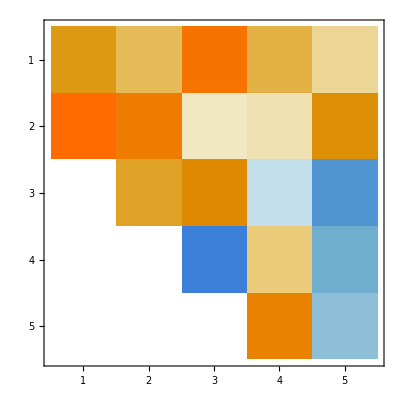
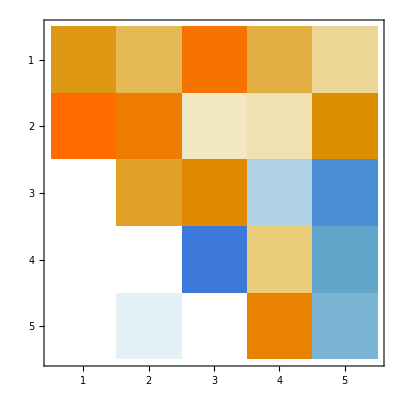

```mathematica
m=5;
A=RandomReal[{-1,1},{m,m}];
{Q,H}=HessenbergDecomposition[A];
Map[Norm,{H-Qᵀ.A.Q, A-Q.H.Qᵀ}]
SignFix1=SparseArray[Band[{1,1}]->Sign[Diagonal[H,-1]],{m,m}];
SignFix2=SparseArray[Band[{2,2}]->Sign[Diagonal[H,-1]],{m,m}];
SignFix=SignFix1.SignFix2;
{QHat,HHat} = {Q.SignFix,H.SignFix};
Map[Norm,{H-QHatᵀ.A.QHat, A-Q.H.Qᵀ}]

Map[MatrixPlot,{H,Qᵀ.A.Q}]
```